```mathematica
(*Avtomatsko shranjevanje notebook-a*)SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Vaje 8 - Podatkovna analiza z Mathematico

1. a) Z ukazom ‘Directory’ preveri delovno področje. Nato z uporabo ‘SetDirectory’ in ‘NotebookDirectory’ nastavi delovno področje na ustrezno mapo.

```mathematica
pot = NotebookDirectory[]
SetDirectory[pot]
Directory[]
```

C:\Users\fk72368\Documents\fork\ROM-2025-26\Vaje 8\

C:\Users\fk72368\Documents\fork\ROM-2025-26\Vaje 8

C:\Users\fk72368\Documents\fork\ROM-2025-26\Vaje 8

1. b) Z ukazom ‘Import’ uvozi tabelo iz datoteke ‘rezultati.xlsx’, v kateri se nahajajo rezultati pisnega izpita pri nekem predmetu. Podatke uvozi v formatu ‘Dataset’. Uvožena tabela naj ima označeno “glavo” (prvo vrstico - ukaz ‘HeaderLines’).  Tabelo shani v spremenljivko ‘podatki’.

```mathematica
podatki = First[Import["rezultati.xlsx", "Dataset", HeaderLines-> 1]]
```

2. Sestavi naslednje funkcije:
 1.) Imena[podatki_], ki vrne seznam imen stolpcev (prva vrstica tabele). Uporabiš lahko funkcijo ‘Keys’.
 2.) Podatki[podatki_], ki vrne tabelo podatkov, t.j. podatke v vrsticah brez glave tabele. Uporabiš lahko funkcijo ‘Values’.
 3.) IndeksStolpca[podatki_, stolpec_], ki za dano ime stolpca vrne indeks stolpca. Npr. pri naši tabeli klic IndeksStolpca[podatki, “Ime”] vrne 2. Če stolpec s tem imenom ne obstaja, naj funkcija vrne Null (prazno). Poskusi uporabiti funkcijo ‘Position’, za definiranje lokalnih spremenljivk pa lahko uporabiš funkcijo ‘Module’.
 4.) Stolpec[podatki_, stolpec_], ki vrne podatke v stolpcu s podanim imenom stolpec. Seznam naj vsebuje samo podatke, ne pa tudi glave. Poskusi uporabiti funkcijo ‘Transpose’.
5.) PovprecjeTock[podatki_], ki izračuna povprečje doseženih točk. Uporabi funkcijo ‘Mean’.
6.) RazlicneVrednosti[podatki_, stolpec_], ki vrne seznam različnih vrednosti za stolpec. Koliko skupin testov so pisali? Namig: preveri, kaj naredi funkcija ‘Union’ na seznamih, v katerih se ponavaljajo vrednosti.
7.) Vrstica[podatki_, i_], ki vrne i-to vrstico v tabeli. Pazi: vrstice z glavo ne šteješ. Vrstica z indeksom 1 je prva naslednja vrstica po glavi, t.j. prva vrstica podatkov.

```mathematica
(*1*)Imena[podatki_]:= First[Keys[podatki]]
Imena[podatki];
```

```mathematica
(*2*)Podatki[podatki_] := Values[podatki]
Podatki[podatki];
```

```mathematica
(*3*)IndeksStolpca[podatki_, stolpec_] := If[MemberQ[Imena[podatki], stolpec ],
										Position[Imena[podatki],stolpec][[1]][[1]],
										Null]
IndeksStolpca[podatki, "Ime"];
```

```mathematica
(*4*) Stolpec[podatki_, stolpec_] := Normal[Module[{n=IndeksStolpca[podatki, stolpec]}, Transpose[podatki][[n]]]]
Stolpec[podatki,"Točke"]
```

{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

```mathematica
(*5*)PovprecjeTock[podatki_] := Mean[Stolpec[podatki, "Točke"]]
PovprecjeTock[podatki];
```

```mathematica
(*6*)RazlicneVrednosti[podatki_, stolpec_] :=  Length[DeleteDuplicates[Stolpec[podatki, stolpec]]]
RazlicneVrednosti[podatki, "Skupina"];
```

3. Sestavi funkcijo OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_], pri kateri so v prvem argumentu meje za ocene v številu točk, v drugem argumentu pa število točk, za katere želimo izračunati oceno. Funkcijo napiši s pomočjo ustreznih stavkov ‘If’. Nato sestavi funkcijo Ocene[podatki_, meje_], ki izračuna stolpec ocen za dane podatke in meje.

```mathematica
OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_] := If[
tocke>=za10,10,
If[tocke>=za9, 9,
If[tocke>=za8,8,
If [tocke>=za7,7,
If[tocke>=za6,6,0]
]
]
]
]
```

```mathematica
Ocene[podatki_, meje_]:=Table[OcenaZaMeje[meje, Stolpec[podatki,"Točke"][[i]]], {i,1,Length[podatki]}]
```

```mathematica
kriterij = {50, 60, 70, 80, 90};
ocene = Ocene[podatki,kriterij]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

4. Sestavi funkcijo DodajStolpec[podatki_], ki obstoječi tabeli doda še en stolpec (oz . vrne novo tabelo z dodanim stolpcem) . Premisli, kako s pomočjo ‘Query’ dodaš stolpec tabeli.  Podatkom dodaj stolpec "Ocena" z ocenami in vse skupaj shrani v spremenljivko podatkiOcene. Novo tabelo shrani v Excelov zvezek ‘ocene.xlsx’ s pomočjo ukaza ‘Export’ .

5. Preveri, kaj naredi funkcija ‘BinCount’ na seznamu ocen. Ali bi se dele rezultata te funkcije dalo uporabiti, da bi prešteli, koliko študentov je dobilo kakšno oceno? Namig : uporabiš lahko funkcije za delo s seznami kot so Rest, Drop, Take, ... Izračunaj porazdelitev ocen in jo shrani v spremenljivko ‘porazdelitevOcen’. To je seznam šestih vrednosti, pri čemer prva predstavlja število študentov z negativno oceno, druga število študentov z oceno 6, . . .

```mathematica
porazdelitevOcen = Drop[BinCounts[ocene, {0,11,1}],{2,6}]
```

```mathematica
{13,2,3,4,2,4}
BinCounts[ocene, {0,11,1}]
```

{13,2,3,4,2,4}

{13,0,0,0,0,0,2,3,4,2,4}

# Vaje 9 - Podatkovna analiza z Mathematico II

6. stolpični diagram

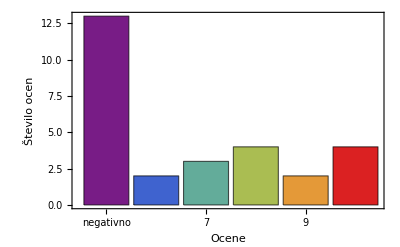

stolpicni.pdf

```mathematica
bar = BarChart[porazdelitevOcen, ChartStyle -> "Rainbow", ChartLabels->{"negativno",6,7,8,9,10}, Frame -> True,FrameLabel->{{"Število ocen", ""}, {"Ocene", "Ocene pri pisnem izpitu"}}]
Export["stolpicni.pdf",bar]
```